```mathematica
ClearAll["Global'*"]
G[r1_,r2_]:=3/40{{r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))},{r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))}};
G2[{r1_,r2_}]:=3/40{{r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))},{r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))}};
G3[{r1_,r2_}]:=3/40{{r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))},{r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))}};
```

```mathematica
g1[r1_,r2_]={r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))};
g2[r1_,r2_]={r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))};
```

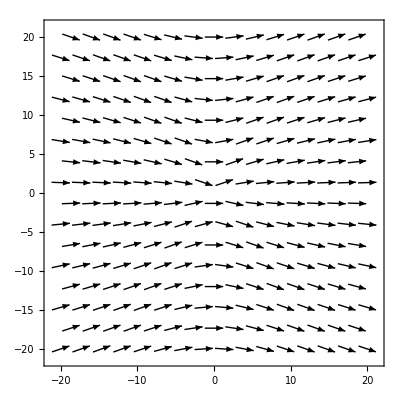

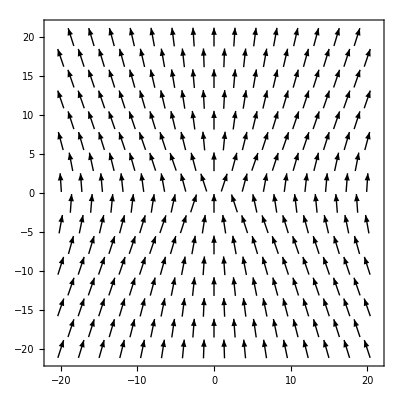

```mathematica
VectorPlot[g1[x,y],{x,-20,20},{y,-20,20}]
VectorPlot[g2[x,y],{x,-20,20},{y,-20,20}]
```

```mathematica
y0:={2,0}
```

```mathematica
y0hat:=y0/Norm[y0];
```

```mathematica
epsilon:=1/Norm[y0]
```

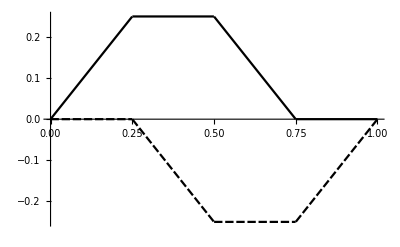

```mathematica
x1[t_]:={0,Piecewise[{{ Mod[t,1],0 ≤ Mod[t,1] ≤ 1/4},{1/4,1/4 ≤ Mod[t,1] ≤ 1/2},{1/4-( Mod[t,1]-1/2),1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}]};
x2[t_]:={Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-( Mod[t,1]-1/4),1/4 ≤ Mod[t,1] ≤ 1/2},{-1/4,1/2≤ Mod[t,1]≤ 3/4},{-1/4 + ( Mod[t,1]-3/4),3/4 ≤ Mod[t,1]≤ 1}}],0};
dx1[t_]:={0,Piecewise[{{1,0 ≤ Mod[t,1] ≤ 1/4},{0,1/4 ≤ Mod[t,1] ≤ 1/2},{-1,1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}]};
dx2[t_]:={Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-1,1/4 ≤ Mod[t,1] ≤ 1/2},{0,1/2≤ Mod[t,1]≤ 3/4},{1,3/4 ≤ Mod[t,1]≤ 1}}],0};
Plot[{x1[t][[2]],x2[t][[1]]},{t,0,1}]
```

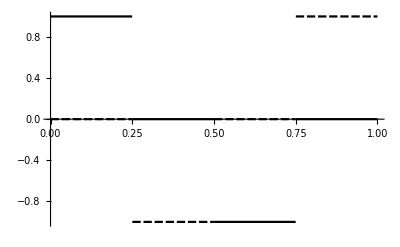

```mathematica
Plot[{dx1[t][[2]],dx2[t][[1]]},{t,0,1}]
```

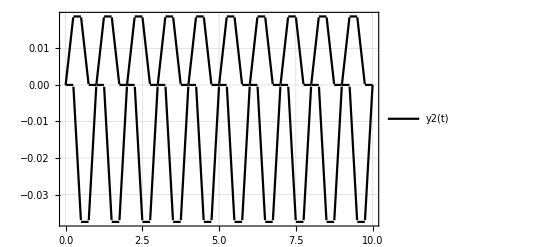

```mathematica
y2[t_]=G2[y0hat].x1[t]+ G2[y0hat].x2[t];
Plot[y2[t],{t,0,10},PlotTheme->"Detailed"]
y22=NDSolveValue[{y'[t]==(3/40)(y0hat.x1[t] dx1[t]+3 y0hat (y0hat.x1[t])(y0hat.dx1[t])+(y0hat.x2[t] )dx2[t]+3 y0hat (y0hat.x2[t])( y0hat.dx2[t]) - y0hat (x1[t].dx1[t])-y0hat (x2[t].dx2[t])-x1[t] (y0hat.dx1[t])-x2[t]( y0hat.dx2[t])),y[0]=={0,0}},y,{t,0,100},Method->{"ImplicitRungeKutta"}];
```

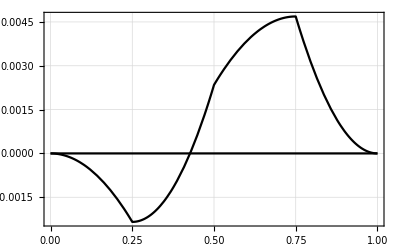

```mathematica
Plot[y22[t],{t,0,1},PlotTheme->"Detailed",PlotLegends->"y_{22}(t)"]
```

```mathematica
x11[t_?NumericQ]:={0,Piecewise[{{ Mod[t,1],0 ≤ Mod[t,1] ≤ 1/4},{1/4,1/4 ≤ Mod[t,1] ≤ 1/2},{1/4-( Mod[t,1]-1/2),1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}]};
x21[t_?NumericQ]:={Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-( Mod[t,1]-1/4),1/4 ≤ Mod[t,1] ≤ 1/2},{-1/4,1/2≤ Mod[t,1]≤ 3/4},{-1/4 + ( Mod[t,1]-3/4),3/4 ≤ Mod[t,1]≤ 1}}],0};
dx11[t_?NumericQ]:={0,Piecewise[{{1,0 ≤ Mod[t,1] ≤ 1/4},{0,1/4 ≤ Mod[t,1] ≤ 1/2},{-1,1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}]};
dx21[t_?NumericQ]:={Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-1,1/4 ≤ Mod[t,1] ≤ 1/2},{0,1/2≤ Mod[t,1]≤ 3/4},{1,3/4 ≤ Mod[t,1]≤ 1}}],0};
y3=NDSolveValue[{b'[t]==G2[b[t]-x11[t]].dx11[t]+G2[b[t]-x21[t]].dx21[t],b[0]==y0},b,{t,0,100},Method->"ImplicitRungeKutta"];
```

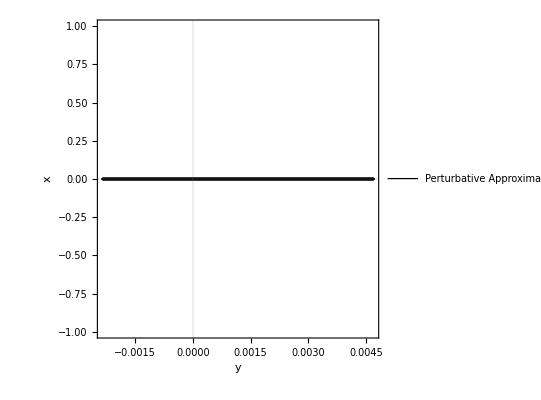

```mathematica
ParametricPlot[{y22[t]},{t,0,1},AspectRatio->1, FrameLabel->{"y","x"},PlotTheme->"Scientific",PerformanceGoal->"Quality",PlotRange->Full,PlotLegends->LineLegend[{"Perturbative Approximation"},LegendFunction->Frame],PlotStyle->{{Black, Thickness[0.005]},{Dashed, Black,Thickness[0.005]}}]
```

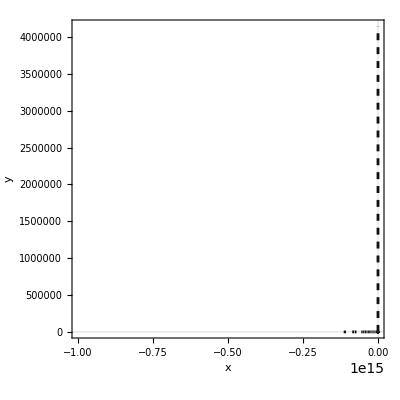

```mathematica
curve=ParametricPlot[{y0+epsilon y2[t]+epsilon^2 y22[t],y3[t]},{t,0,100},AspectRatio->1, FrameLabel->{"x","y"},PlotTheme->"Scientific",PerformanceGoal->"Quality",PlotRange->Full,PlotStyle->{{Black, Thickness[0.005]},{Dashed, Black,Thickness[0.005]}}]
```

```mathematica
dd1 =epsilon^2(y22[1.0]-y22[0])
y2[1]-y2[0]
dd2=y3[1]-y3[0]
displ[h_]:=epsilon^2(3/64 )(1-h[[2]]^2/Norm[h]^2)h/Norm[h]^3
N[displ[y0]]
```

{9.26078×10^-11,0.}

{0,0}

{5.89923×10^-6,-0.000124454}

{0.00292969,0.}

```mathematica
curve2=ParametricPlot[{x1[t],x2[t]},{t,0,1}];
```

```mathematica
Animate[{Show[curve2,Graphics[{PointSize[Large],Point[x1[t]],Point[x2[t]]}]],Show[curve,Graphics[{PointSize[Large],Point[y0+epsilon y2[t]+epsilon^2 y22[t]]}]]},{t,0,1},RefreshRate->30];
```